## Uses shortest path algorithms to find an optional path for 2 robots actuated by global inputs

### Idea Base case 1: deltaX and deltaY are 0, simply move robots to final position Base case 2: In 2 moves we can make both deltaX and deltaY 0, implement this move, then call Base case 1: We build a list like in an A* algorithm. Each item in the list has 4 entries, and the list is sorted based on the first entry: {estimatedPathLength, r1, r2, MOVES} MOVES is the moves that have been applied to the robots: {{x1,y1},{x2,y2}} for a two move sequence. r1 and r2 are the positions of robot 1 and 2 after applying MOVES to them. estimatedPathLength is the sum of the euclidean distances of MOVES + an admissible heuristic (the maximum distance of r1 or r2 from their goal positions). How the solver works: Start with start positions s1,s2 and goal positions g1, g2. optimalPathList = { {Max( distance(g1,s1), distance(g2,s2) ), s1,s2, {} } While forever if the first item in optimalPathList, the estimatedPathLength == sum of the euclidean distances of MOVES, we have the optimal solution, so return the MOVES for the first item else Pop the first item from the list, call {move1, move2, r1new, r2new} = wallFrictionMove(direction, r1, r2, g1, g2) for the 4 walls if already in contact with one wall, also try a DRIFT_move. Add all the new moves to optimalPathList end while wallFrictionMove(direction, r1, r2, g1, g2) should first see if Base case 1: is possible, next see if Base case 2 is possible, else try to reduce deltaX and deltaY. We will need to ensure that the robots never overlap, which means that wallFrictionMove might return several options. (g2x-g1x)= Δgx (r2x-r1x)= Δrx Δgx-Δrx = Δex

```mathematica
(*Equation*)
admissibleHeuristic[s1_,s2_, g1_,g2_]:=Max[Abs[EuclideanDistance[g1,s1]],Abs[EuclideanDistance[g2,s2]]] (* a distance measurement that never over estimates to possible distance *) 

(* wallFrictionMoveDir just rotates or unrotates the coordinate frame*)
wallFrictionMoveDir[dir_,s1_,s2_,g1_,g2_,moves_,pm1_, pm2_, ϵ_]:=Module[{Δex, Δey, path = moves, path1= pm1, path2= pm2},
(*
s1 = starting position of robot 1 for this move;
s2 = starting position of robot 2 for this move;
moves to contact wall in direction dir.


  If one robot is already touching the wall in direction dir, just moves the second robot. 
 Movements are chosen to minimize |Δex| and |Δey|, the error from the desired spacing of the robots, where Δex = (g2x-g1x) - (r2x-r1x)  and Δey = (g2y-g1y) - (r2y-r1y) .  If robots would end up overlapping, returns multiple possibilities +/- ϵ  *)

(*STEP 1: is base case 1 possible?  If so, do it and return*)
{Δex, Δey} = (g2-g1)-(s2-s1);
If[-0.00001≤ Δex≤ 0.00001 && -0.00001≤ Δey < 0.00001,
AppendTo[path, {g2⟦1⟧-  s2⟦1⟧, g2⟦2⟧- s2⟦2⟧}];AppendTo[path1,  g1]; AppendTo[path2, g2];
Return[ { distanceMoved[ path],g1,g2,path,path1,path2, True }  ]];

(*OTHERWISE, move in the desired direction to contact a wall.  
We'll need to rotate the coordinate frames so the movement is up, and ensure robot 1 is the first to contact.
then we'll call wallFrictionMoveUp, 
then we take the answer, and reassign robot 1 and 2 to match original
then rotate answer into original coordinate frame*)
Module[{r1,r2,newPathEntries,s1t,s2t,g1t,g2t,movest, pm1st, pm2st},
(* if move is up, call wallFrictionMoveUp, otherwise rotate frame, then unrotate answers*)
If[dir=="u", 
(*Print["up selected:"];*)
newPathEntries= wallFrictionMoveUp[s1,s2,g1,g2,moves,pm1, pm2,ϵ];

];
(* if move is down, rotate frame 180 deg, then unrotate answers*)
If[dir=="d", 
{s1t,s2t,g1t,g2t}= Map[rotate180,{s1,s2,g1,g2}];
movest= Map[rotate180inplace,moves];
pm1st= Map[rotate180,pm1];
pm2st= Map[rotate180,pm2];
newPathEntries= wallFrictionMoveUp[s1t,s2t,g1t,g2t,movest,pm1st, pm2st,ϵ];
(*undo the change*)
newPathEntries⟦2⟧ = rotate180[newPathEntries⟦2⟧];
newPathEntries⟦3⟧ = rotate180[newPathEntries⟦3⟧ ];
newPathEntries⟦4⟧ = Map[rotate180inplace, newPathEntries⟦4⟧ ];
newPathEntries⟦5⟧ = Map[rotate180, newPathEntries⟦5⟧ ];
newPathEntries⟦6⟧ = Map[rotate180, newPathEntries⟦6⟧ ];

];
(* if move is right, rotate frame 90 deg, then unrotate answers*)
If[dir=="r", 
{s1t,s2t,g1t,g2t}= Map[rotate90,{s1,s2,g1,g2}];
movest= Map[rotate90inplace,moves];
pm1st= Map[rotate90,pm1];
pm2st= Map[rotate90,pm2];
newPathEntries= wallFrictionMoveUp[s1t,s2t,g1t,g2t,movest,pm1st, pm2st,ϵ];
(*undo the change*)
newPathEntries⟦2⟧ = rotate270[newPathEntries⟦2⟧];
newPathEntries⟦3⟧ = rotate270[newPathEntries⟦3⟧ ];
newPathEntries⟦4⟧ = Map[rotate270inplace, newPathEntries⟦4⟧ ];
newPathEntries⟦5⟧ = Map[rotate270, newPathEntries⟦5⟧ ];
newPathEntries⟦6⟧ = Map[rotate270, newPathEntries⟦6⟧ ]
];
(* if move is left, rotate frame 270 deg, then unrotate answers*)
If[dir=="l", 
{s1t,s2t,g1t,g2t}= Map[rotate270,{s1,s2,g1,g2}];
movest= Map[rotate270inplace,moves];
pm1st= Map[rotate270,pm1];
pm2st= Map[rotate270,pm2];
newPathEntries= wallFrictionMoveUp[s1t,s2t,g1t,g2t,movest,pm1st, pm2st,ϵ];
(*undo the change*)
newPathEntries⟦2⟧ = rotate90[newPathEntries⟦2⟧];
newPathEntries⟦3⟧ = rotate90[newPathEntries⟦3⟧ ];
newPathEntries⟦4⟧ = Map[rotate90inplace, newPathEntries⟦4⟧ ];
newPathEntries⟦5⟧ = Map[rotate90, newPathEntries⟦5⟧ ];
newPathEntries⟦6⟧ = Map[rotate90, newPathEntries⟦6⟧ ]
];
Return [newPathEntries]
](*end inner module*)

](*end outer module*)

(* Algorithm wallFrictionMoveUp *)
wallFrictionMoveUp[r1in_,r2in_,g1in_,g2in_,moves_,pm1_, pm2_ , ϵ_]:= 

Module[{r1,r2,g1,g2,Δgx,Δgy,m1,m2,r1out,r2out,Δtgx,Δtgy,
Δey ,Δex ,
L= 1 (*size of workspace*),
path1= pm1(*desired moves for r1*),
path2= pm2(*desired moves for r2*),
path ,
isMirrored = False,
isFlipped = False
},
(*robot 1 must be the top left robot. If it is not the top robot, flip entries, if it is not the left robot, mirror entries. Remember to switch again at end!
 then move robot  while first robot is touching wall*)
{r1,r2,g1,g2,isMirrored,isFlipped,path}= ensurer1r2[r1in,r2in,g1in,g2in,moves];
{Δgx,Δgy} = g2-g1;
(*If the second robot is already touching the up wall, just return.*)
If[r2⟦2⟧== 1, Return [{Infinity, r1, r2, path, path1, path2 , False}]];
(*if the goal Δgx,Δgy is achievable, do it in one move. Otherwise, *) 
If[r2⟦1⟧- r1⟦1⟧-1(*+2ϵ*)>   Δgx , Δtgx = r2⟦1⟧- r1⟦1⟧-1(*+2ϵ*),  Δtgx =  Δgx];
If[ Δgy > 0,  Δtgy = 0, Δtgy = Δgy];
If[Δgy  < r2⟦2⟧- r1⟦2⟧,  Δtgy = r2⟦2⟧- r1⟦2⟧,, Δtgy = Δgy];

If[r2⟦1⟧- r1⟦1⟧-1+ 2ϵ≤  Δtgx ≤  1 -2ϵ && r2⟦2⟧- r1⟦2⟧ ≤ Δtgy≤  0,

(*in Achievable range*)

(*move r1 and r2 so that r1 will touch the up wall in the line of the goal*)
m1={(1-r1⟦2⟧)/(2-g1⟦2⟧- r1⟦2⟧)(g1⟦1⟧-r1⟦1⟧),1-r1⟦2⟧};
,
(*not in achievable range*)

(*move the shortest path to the wall*)
 m1 = {0,1- r1⟦2⟧};
];
(*Check the boundaries*)
If[r2⟦1⟧+ m1⟦1⟧ >1 , m1⟦1⟧ = 1-r2⟦1⟧];
If[r1⟦1⟧+ m1⟦1⟧<0, m1⟦1⟧ = -r1⟦1⟧];

If[r1⟦1⟧+m1⟦1⟧+Δtgx > 1&& Δtgx >0, m1⟦1⟧-= Δtgx + r1⟦1⟧+ m1⟦1⟧-1];

If[r1⟦1⟧+m1⟦1⟧+Δtgx<0 && Δtgx<0,m1⟦1⟧ += Abs[Δtgx]-r1⟦1⟧-m1⟦1⟧];


If[r1⟦2⟧ == 1, m1 = {0,0}, If[ m1⟦1⟧==0,  If[r1⟦1⟧== 1 || r2⟦1⟧== 1, m1⟦1⟧-= ϵ]; If[r1⟦1⟧== 0|| r2⟦1⟧== 0, m1⟦1⟧ += ϵ]]];

r1 += m1; r2+= m1;

{Δex, Δey} = {Δtgx, Δtgy}-(r2-r1);

(*move r2 to get correct spacing*)
If[Δex ≥  0 , m2 = {Min[Δtgx-(r2⟦1⟧-r1⟦1⟧), 1-r2⟦1⟧],Δtgy-(r2⟦2⟧-r1⟦2⟧) }, m2 = {Max[Δtgx-(r2⟦1⟧-r1⟦1⟧), -r2⟦1⟧],Δtgy-(r2⟦2⟧-r1⟦2⟧) }];
(*Check if the robots are in ϵ difference with each other*)
If[r1⟦1⟧-ϵ/2≤ r2⟦1⟧ +m2⟦1⟧ ≤ r1⟦1⟧+ϵ/2&& r1⟦2⟧==  r2⟦2⟧+ m2⟦2⟧ , If[r2⟦1⟧+ m2⟦1⟧>  L/2, m2⟦1⟧ +=r1⟦1⟧+ϵ-r2⟦1⟧- m2⟦1⟧, m2⟦1⟧ +=r1⟦1⟧-ϵ-r2⟦1⟧- m2⟦1⟧]];

If[r2⟦2⟧ == 1, m2 = {0,0}];



If[m1≠ {0,0},
(*Add m1*)
AppendTo[path, m1];
{r1out,r2out}=  returnr1r2[isFlipped,isMirrored, r1,r2];
AppendTo[path1, r1out];
AppendTo[path2,r2out];];
(*Add m2*)
r2 += m2;
AppendTo[path, m2];
{r1out,r2out}=  returnr1r2[isFlipped,isMirrored, r1,r2];
AppendTo[path1, r1out];
AppendTo[path2,r2out];
(*Change the path back if it was mirrored*)
If[isMirrored,
path = Map[mirrorInplace, path];
];

Return[{If[ -0.00001<m2⟦1⟧<0.00001 && -0.00001<m2⟦2⟧<0.00001, Infinity,distanceMoved[ path]],r1out,r2out,path,path1,path2 ,False }  ]
]

(*Undoing the mirroring and flipping*)
returnr1r2[isFlipped_,isMirrored_, r1_,r2_]:=Module[{r1out, r2out},If[isMirrored,If[isFlipped,r1out= mirror[r2];r2out=mirror[r1],r1out= mirror[r1]; r2out = mirror[r2]],If[isFlipped,r1out= r2; r2out=r1,r1out=r1;r2out=r2]];
Return [{r1out,r2out}]]
(*Doing mirroring and flipping*)
ensurer1r2[r1in_, r2in_,g1in_,g2in_,moves_]:=Module[{r1,r2,isFlipped,isMirrored,g1,g2,path},
isFlipped= False;
isMirrored= False;
If[r1in⟦2⟧<r2in⟦2⟧,
If[r1in⟦1⟧>r2in⟦1⟧,
{r1,r2,g1,g2}={r2in,r1in,g2in,g1in};
isFlipped = True; path = moves,
{r1,r2,g1,g2}= Map[mirror, {r2in,r1in,g2in,g1in}];
path = Map[mirrorInplace, moves];

isFlipped = True;
isMirrored = True],

If[r1in⟦1⟧>r2in⟦1⟧,
{r1,r2,g1,g2}= Map[mirror, {r1in,r2in,g1in,g2in}];
path = Map[mirrorInplace, moves];
isMirrored= True,
{r1,r2,g1,g2}={r1in,r2in,g1in,g2in};
path= moves
];

];
Return[{r1,r2,g1,g2,isMirrored,isFlipped,path}]]
(*rotate the coordinate frame 270 degrees*)
rotate270[r_]:={1- r⟦2⟧, r⟦1⟧}
(* changes in path when we rotate 270 degrees*)
rotate90inplace[r_]:={ r⟦2⟧, -r⟦1⟧}
(*rotate the coordinate frame 90 degrees*)
rotate90[r_] := {r⟦2⟧,1- r⟦1⟧}
(* changes in path when we rotate 90 degrees*)
rotate270inplace[r_] := {-r⟦2⟧, r⟦1⟧}
(*rotate the coordinate frame 180 degrees*)
rotate180[r_] := {1-r⟦1⟧,1- r⟦2⟧}
(* changes in path when we rotate 180 degrees*)
rotate180inplace[r_] := {-r⟦1⟧,- r⟦2⟧}
(* mirror the coordinate frame about the right wall*)
mirror[r_] := {1-r⟦1⟧,r⟦2⟧}
(* changes in path when we mirror*)
mirrorInplace[r_]:= {-r⟦1⟧,r⟦2⟧}
(*Total distance moved with the sequence of moves*)
distanceMoved[moves_]:= Total[Table[Norm[m],{m,moves}]]
```

```mathematica
optimal2robotPath, the top level algorithm
```

```mathematica
(*Function that does an A* search to find the shortest path*)
optimal2robotPath[s1_,s2_, g1_,g2_,ϵ_]:=Module[{optimalPathList
,pathToExplore,r1,r2,wallMoves,moves,pm1, pm2
},
pathToExplore= {Infinity,s1,s2,{{0,0}},{s1},{s2},False};
optimalPathList={pathToExplore};
While[pathToExplore⟦7⟧ ≠  True,
(*body of while loop*)
r1 = pathToExplore⟦2⟧;
r2 = pathToExplore⟦3⟧;

moves= pathToExplore⟦4⟧;
pm1 = pathToExplore⟦5⟧;
pm2 = pathToExplore⟦6⟧;

Table[
wallMoves = wallFrictionMoveDir[dir,r1,r2,g1,g2,moves,pm1, pm2, ϵ];
optimalPathList=AppendTo[optimalPathList,wallMoves];,
{dir,{"u","d","l","r"}}];
optimalPathList = SortBy[optimalPathList, First];(*sorts the current list by their total distance moved*)
pathToExplore = First[optimalPathList]; (*read first entry*)
optimalPathList= Delete[optimalPathList,1];(*pop off first entry*)

];
(*return the best movement*)
Return[{optimalPathList⟦1⟧⟦4⟧, optimalPathList⟦1⟧⟦5⟧, optimalPathList⟦1⟧⟦6⟧}]
]
```

```mathematica
s1a = {1/4,3/4};
g1a = {3/4,1/4};
s2a={3/4,3/4};
r = 1/40;
ϵ =0.001;
step = 0.01;
s1b = {1/10,9/10};
g1b = {9/10,0.1};
s2b={9/10,0.1};
s1c = {3/4,0.4};
g1c = {5/10,0.5};
s2c={1/4,2/10};
numMoves7a2=Flatten[Table[{x,y,Length[First@optimal2robotPath[s1a,s2a, g1a,{x,y},ϵ]]-1},{x,ϵ,1-ϵ,step},{y,ϵ,1-ϵ,step}],1];
numMoves7b2=Flatten[Table[{x,y,Length[First@optimal2robotPath[s1b,s2b, g1b,{x,y},ϵ]]-1},{x,ϵ,1-ϵ,step},{y,ϵ,1-ϵ,step}],1];
numMoves7c2=Flatten[Table[{x,y,Length[First@optimal2robotPath[s1c,s2c, g1c,{x,y},ϵ]]-1},{x,ϵ,1-ϵ,step},{y,ϵ,1-ϵ,step}],1];
```

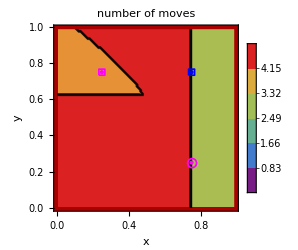
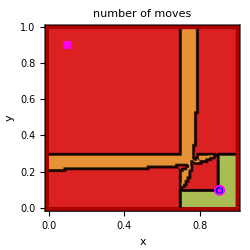
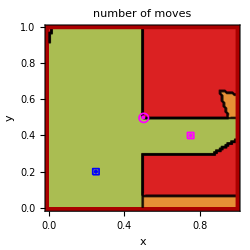

```mathematica
upperBound2 = 5;
LowerBound2 =0;
bl1=BarLegend[{"Rainbow",{LowerBound2,upperBound2}},5];
PointSize[0.01];
lcp11=ListContourPlot[numMoves7a2,InterpolationOrder->1,ImageSize->250,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{LowerBound2,upperBound2}}],FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves"];
lcp21=ListContourPlot[numMoves7b2,InterpolationOrder->1,ImageSize->250,(*PlotRange-> {{0,1},{0,1},{0,7}},*)ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{LowerBound2,upperBound2}}],FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves"];
lcp31=ListContourPlot[numMoves7c2,InterpolationOrder->1,ImageSize->250,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{LowerBound2,upperBound2}}],FrameLabel->{"x","y"},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily-> "Times"], PlotLabel->"number of moves"];
nums7a2 = 
Show[lcp11,Epilog->{Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}], Magenta,Point[{s1a}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1a-2/3r {1,1},s1a+2/3r{1,1}], Blue,Point[{s2a}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2a-2/3r {1,1},s2a+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1a}], Magenta,Thickness[0.005], Circle[g1a,r]} ];
nums7b2 =Show[lcp21,Epilog->{Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}],Magenta,Point[{s1b}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1b-2/3r {1,1},s1b+2/3r{1,1}], Blue,Point[{s2b}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2b-2/3r {1,1},s2b+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1b}], Magenta,Thickness[0.005], Circle[g1b,r]} ];
nums7c2 =Show[lcp31,Epilog->{Darker[Red],Rectangle[-0.025{1,1},{0,1.025}],Rectangle[{-0.025,1-0.0125},{1.025,1.025}],Rectangle[-0.025{1,1},{1.025,0}],Rectangle[{1-0.0125,-0.025},{1.025,1.025}], Magenta,Point[{s1c}],EdgeForm[Directive[Magenta,Thickness[0.005]]],FaceForm[None],Rectangle[s1c-2/3r {1,1},s1c+2/3r{1,1}], Blue,Point[{s2c}],EdgeForm[Directive[Blue,Thickness[0.005]]],FaceForm[None],Rectangle[s2c-2/3r {1,1},s2c+2/3r{1,1}], Magenta,Thickness[0.005],Point[{g1c}], Magenta,Thickness[0.005], Circle[g1c,r]} ];

Legended[Row[{nums7a2,nums7b2,nums7c2},Spacer[7]],bl1]
```